```mathematica
Solve[y5^2+3^2==5^2,y5]
```

{{y5→-4},{y5→4}}

```mathematica
Solve[y4^2+3^2==4^2,y4]
```

{{y4→-√7},{y4→√7}}

```mathematica
Solve[{y==4x/3,y==-(Sqrt[7] x)/3+Sqrt[7]},{x,y}]
```

{{x→(3 √7)/(4+√7),y→(4 √7)/(4+√7)}}

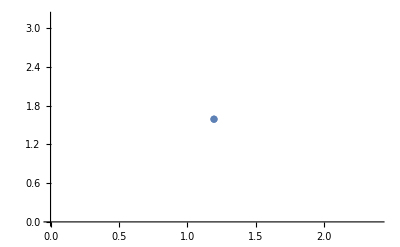

```mathematica
ListPlot[{{(3 √7)/(4+√7),(4 √7)/(4+√7)}}]
```

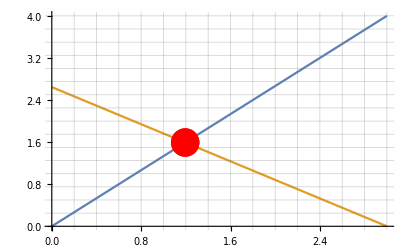

```mathematica
Show[Plot[{4x/3,-(Sqrt[7] x)/3+Sqrt[7]},{x,0,3},GridLines->All, GridLines->Directive[Red]],ListPlot[{{(3 √7)/(4+√7),(4 √7)/(4+√7)}}, PlotStyle->Directive[PointSize[.05],Red]]]
```